```mathematica
FileExport[data_, filename_?StringQ, parser_?StringQ] :=
With[
{folder=FileNameJoin[{ParentDirectory@NotebookDirectory[], "LaTeX", "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,filename}] , data, parser];
];
```

```mathematica
(*Исходные данные*)
EE=1;(*2.1*10^11;*)
d=10/1000;
J=1;(*Pi*d^4/64;*)
l=1;
t0 = -1*Pi/180; (*заданный поворот в заделке*)
u0 = 0; (*заданное перемещение левого края*)
uk = 0; (*заданное перемещение правого края*)
tk = 0;
q = -1; (*интенсивность распределенной нагрузки Н/м*)
z0=l/2;

StifMtr[L_,EE_,J_]:={{(5092 EE*J)/(35 L^3),(1138 EE*J)/(35 L^2),-(512 EE*J)/(5 L^3),(384 EE*J)/(7 L^2),-(1508 EE*J)/(35 L^3),(242 EE*J)/(35 L^2)},{(1138 EE*J)/(35 L^2),(332 EE*J)/(35 L),-(128 EE*J)/(5 L^2),(64 EE*J)/(7 L),-(242 EE*J)/(35 L^2),(38 EE*J)/(35 L)},{-(512 EE*J)/(5 L^3),-(128 EE*J)/(5 L^2),(1024 EE*J)/(5 L^3),0,-(512 EE*J)/(5 L^3),(128 EE*J)/(5 L^2)},{(384 EE*J)/(7 L^2),(64 EE*J)/(7 L),0,(256 EE*J)/(7 L),-(384 EE*J)/(7 L^2),(64 EE*J)/(7 L)},{-(1508 EE*J)/(35 L^3),-(242 EE*J)/(35 L^2),-(512 EE*J)/(5 L^3),-(384 EE*J)/(7 L^2),(5092 EE*J)/(35 L^3),-(1138 EE*J)/(35 L^2)},{(242 EE*J)/(35 L^2),(38 EE*J)/(35 L),(128 EE*J)/(5 L^2),(64 EE*J)/(7 L),-(1138 EE*J)/(35 L^2),(332 EE*J)/(35 L)}};
KglobStiff[n_,AllLength_,Emodule_,J_]:=Module[{Kglob},
Kglob=Table[0,{i,1,(2*n+1)*2},{j,1,(2*n+1)*2}];
Do[
Do[
    Do[
        Kglob[[i+4*(count-1),j+4*(count-1)]]+=StifMtr[AllLength/n,Emodule,J][[i,j]],
       {j,1,6}
       ],
   {i,1,6}
  ],
{count, 1,n}
];
Kglob
];

SolvingModuleFEM[n_,l_,EE_,J_,q_,t0_]:=Module[{Kstiff,ForceVec,NumOfDOF,Lelem,DispVec,sol,f1,f2,f3,f4,f5,f6,ElemLoad,loadLoc,tmpLoad,count},
loadLoc[z_,zStart_]:=If[z+zStart≤z0,q*Sin[Pi*(z+zStart)/z0],q*Sin[Pi*((z+zStart)-z0)/z0]]; 
f1[z_,Lelem_]:=1-(23 z^2)/Lelem^2+(66 z^3)/Lelem^3-(68 z^4)/Lelem^4+(24 z^5)/Lelem^5;
f2[z_,Lelem_]:=z-(6 z^2)/Lelem+(13 z^3)/Lelem^2-(12 z^4)/Lelem^3+(4 z^5)/Lelem^4;
f3[z_,Lelem_]:=(16 z^2)/Lelem^2-(32 z^3)/Lelem^3+(16 z^4)/Lelem^4;

f4[z_,Lelem_]:=-(8 z^2)/Lelem+(32 z^3)/Lelem^2-(40 z^4)/Lelem^3+(16 z^5)/Lelem^4;
f5[z_,Lelem_]:=(7 z^2)/Lelem^2-(34 z^3)/Lelem^3+(52 z^4)/Lelem^4-(24 z^5)/Lelem^5;
f6[z_,Lelem_]:=-z^2/Lelem+(5 z^3)/Lelem^2-(8 z^4)/Lelem^3+(4 z^5)/Lelem^4;

count = 5;
tmpLoad={};
NumOfDOF=(2*n+1)*2;
Lelem=l/n;
Kstiff=Table[0,{i,1,NumOfDOF},{j,1,NumOfDOF}];
Kstiff=KglobStiff[n,l,EE,J];
ForceVec=Table[0,{i,1,NumOfDOF}];
(*добавление распределенной нагрузки по всей длине*)

ElemLoad [zStart_]:=NIntegrate[loadLoc[z,zStart]*{f1[z,Lelem],f2[z,Lelem],f3[z,Lelem],f4[z,Lelem],f5[z,Lelem],f6[z,Lelem]},{z,0,Lelem},WorkingPrecision->17,AccuracyGoal->15,PrecisionGoal->15];
Do[
AppendTo[tmpLoad,ElemLoad [(i-1)*Lelem]],
{i,1,n,1}
];
(*Print[tmpLoad];*)
tmpLoad=Flatten[tmpLoad];
Do[
ForceVec[[count]]=tmpLoad[[j]]+tmpLoad[[j+2]];
ForceVec[[count+1]]=tmpLoad[[j+1]]+tmpLoad[[j+1+2]];
count = count +4,
{j,5,Length[tmpLoad]-2,6}
];

count =3;
Do[
ForceVec[[count]]=tmpLoad[[j]];
ForceVec[[count+1]]=tmpLoad[[j+1]];
count = count +4,
{j,3,Length[tmpLoad]-2,6}
];

ForceVec[[1]]=tmpLoad[[1]];
ForceVec[[2]]=tmpLoad[[2]];
ForceVec[[-1]]=tmpLoad[[-1]];
ForceVec[[-2]]=tmpLoad[[-2]];

(*Print[ForceVec];*)
(*заготовка вектора перемещений в виде некоторых неизвестных*)
DispVec=Table[u[i],{i,1,NumOfDOF}];
(*Учёт кинематических граничных условий*)
(*ForceVec=ForceVec-Kstiff[[All,2]]*t0-Kstiff[[All,1]]*u0-Kstiff[[All,-2]]*uk; *)
ForceVec=ForceVec-Kstiff[[All,1]]*u0-Kstiff[[All,2]]*t0-Kstiff[[All,-2]]*uk-Kstiff[[All,-1]]*tk; (*коррекция вектора узловых сил для учета поворота в заделке, чтобы использовать метод крестика для учета ГУ*)
(*ForceVec[[2]]=t0; (*коррекция вектора узловых усилий, чтобы поворот в заделке был равен t0*)*)
ForceVec[[1]]=u0; (*коррекция вектора узловых усилий, чтобы перемещение слева было u0*)
ForceVec[[2]]=t0;
ForceVec[[-2]]=uk; (*коррекция вектора узловых усилий, чтобы перемещение справа было uк*)
ForceVec[[-1]]=tk;
Kstiff[[1;;2,All]]=0;
Kstiff[[All,1;;2]]=0;
Kstiff[[1,1]]=1;
Kstiff[[2,2]]=1;
Kstiff[[-2;;-1,All]]=0;
Kstiff[[All,-2;;-1]]=0;
Kstiff[[-2,-2]]=1;
Kstiff[[-1,-1]]=1;
sol=NSolve[Kstiff.DispVec==ForceVec,DispVec]//First;
DispVec=Evaluate[DispVec/.sol]
]

PrecisionSol[l_,EE_,J_,q_,t0_]:=Module[{Sys,solPrec,tmp},
Sys=
{
EE*J*y''''[z]==If[z≤z0,q*Sin[Pi*z/z0],q*Sin[Pi*(z-z0)/z0]],
y[0]==u0,
y'[0]==t0,
y[l]==uk,
y'[l]==tk
};
solPrec=DSolve[Sys,y[z],z]//First;
Print[solPrec];
tmp=Evaluate[y[z]/.solPrec]
]
```

{0.,-0.0174533,-0.0020051042275498,-0.014109858930953,-0.0034209949212863,-0.0082460843191111,-0.0040311857318248,-0.0015317598952026,-0.0038395255555335,0.0043633231299858,-0.0030085318732344,0.0086221599814295,-0.0017847487475417,0.010427745884104,-0.0005733888255232,0.0081102896272229,0.,0.}

{y[z]→(90 z-4 π^4 z-180 z^2-45 π^2 z^2+8 π^4 z^2+60 π^2 z^3-4 π^4 z^3+720 π^3 (Piecewise[{{-Sin[2 π z]/(16 π^4), z≤1/2}, {-1/(8 π^3)+(1/6 π^2 (1-2 z)^3+2 z+Sin[2 π z]/(2 π))/(8 π^3), True}}]))/(720 π^3)}

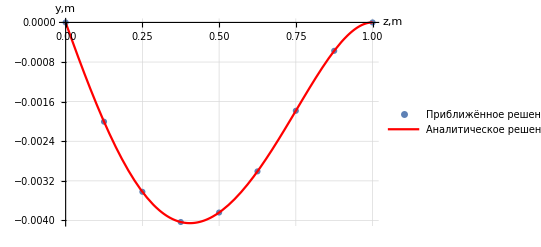

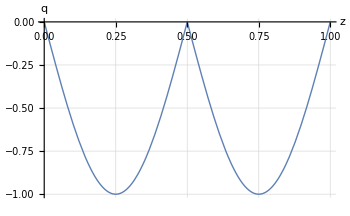

{y[z]→1/(720 π^3)(90 z-4 π^4 z-180 z^2-45 π^2 z^2+8 π^4 z^2+60 π^2 z^3-4 π^4 z^3+720 π^3 (Piecewise[{{-Sin[2 π z]/(16 π^4), z≤1/2}, {-1/(8 π^3)+(1/6 π^2 (1-2 z)^3+2 z+Sin[2 π z]/(2 π))/(8 π^3), True}}]))}

OptionValue::nodef: Unknown option PlotLegends for Graphics.

```mathematica
NElem=4;
UFEM=SolvingModuleFEM[NElem,l,EE,J,q,t0]
yFEMTmp=Table[UFEM[[i]],{i,1,(2*NElem+1)*2,2}];
xFem=Table[(i-1)*l/NElem/2,{i,1,(2*NElem+1)}];
yFEM = Table[{xFem[[i]],yFEMTmp[[i]]},{i,1,Length[xFem]}];
yfunc=PrecisionSol[l,EE,J,q,t0];
pic1=ListPlot[yFEM,GridLines->Automatic,PlotMarkers->Automatic,AxesLabel->{"z,m","y,m"},PlotRange->All,AxesStyle->32,LabelStyle->Directive[Black,Large],PlotLegends-> {"Приближённое решение"}];
pic2=Plot[yfunc/.z->x,{x,0,l},GridLines->Automatic,AxesLabel->{"z,m","y,m"},PlotStyle->{Thick,Red},AxesStyle->32,LabelStyle->Directive[Black,Large],PlotLegends-> {"Аналитическое решение"}];
Show[pic1,pic2,AxesStyle->32,LabelStyle->Directive[Black,Large],PlotLegends-> {"Приближённое решение","Аналитическое решение"}]
qZ = Plot[If[z≤z0,q*Sin[Pi*z/z0],q*Sin[Pi*(z-z0)/z0]],{z,0,l},GridLines->Automatic,AxesLabel->{"z","q"},PlotStyle->{Thick},
LabelStyle->Directive[Black,18, FontFamily -> "Times"],PlotRange->All, GridLines-> Automatic,ImageSize->350]
FileExport[qZ, "q_cont_in.pdf", "PDF"]
```

(1/(8 π^3)-π/180) z+(-1/(4 π^3)-1/(16 π)+π/90) z^2+(1/(12 π)-π/180) z^3+(Piecewise[{{-Sin[2 π z]/(16 π^4), 2 z≤1}, {(-π (-6+π^2 (1-2 z)^2) (-1+2 z)+3 Sin[2 π z])/(48 π^4), True}}])

{2,8.1671641932416×10^-7}

{4,9.7995697468247×10^-9}

{8,1.4502788968855×10^-10}

{16,1.7380008102099×10^-12}

{32,9.8170016781166×10^-14}

{{2,8.1671641932416×10^-7},{4,9.7995697468247×10^-9},{8,1.4502788968855×10^-10},{16,1.7380008102099×10^-12},{32,9.8170016781166×10^-14}}

{2,8.1671641932416×10^-7}

{4,9.7995697468247×10^-9}

{8,1.4428151857521×10^-10}

{16,1.7380008102099×10^-12}

{32,9.8170016781166×10^-14}

{{2,8.1671641932416×10^-7},{4,9.7995697468247×10^-9},{8,1.4428151857521×10^-10},{16,1.7380008102099×10^-12},{32,9.8170016781166×10^-14}}

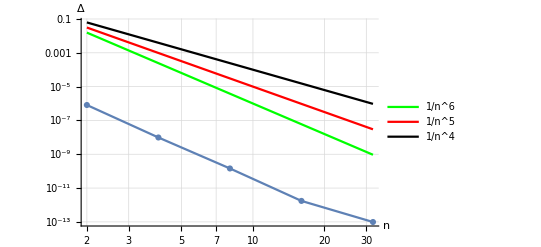

```mathematica
Yt[z_]:=1/(720 π^3)(90 z-4 π^4 z-180 z^2-45 π^2 z^2+8 π^4 z^2+60 π^2 z^3-4 π^4 z^3+720 π^3 (Piecewise[{{-Sin[2 π z]/(16 π^4), z≤1/2}, {-1/(8 π^3)+(1/6 π^2 (1-2 z)^3+2 z+Sin[2 π z]/(2 π))/(8 π^3), True}}]));
Collect[Expand[FullSimplify[Yt[z]]],z]
yFEMfunc[l_,nElem_,UFEM_]:=Module[{N1,N2,N3,N4,N5,N6,Lelem,u1,v1,u2,v2,u3,v3},
Lelem=l/nElem;
N1[x1_,x2_,x3_,z_]:=Piecewise[{{((x2-z)^2 (x3-z)^2 (5 x1^2+x2 x3-3 x1 (x2+x3)-4 x1 z+2 (x2+x3) z))/((x1-x2)^3 (x1-x3)^3),x1≤z<=x3}},0];    (*Функции Эрмита (стыковочные функции Эрмита)*)
N2[x1_,x2_,x3_,z_]:=Piecewise[{{-((x1-z)^2 (x3-z)^2 (-3 x1 x2+5 x2^2+x1 x3-3 x2 x3+2 (x1-2 x2+x3) z))/((x1-x2)^3 (x2-x3)^3),x1≤z<=x3}},0];
N3[x1_,x2_,x3_,z_]:=Piecewise[{{-((x1-z)^2 (x2-z)^2 (x1 x2-3 x1 x3-3 x2 x3+5 x3^2+2 (x1+x2-2 x3) z))/((x1-x3)^3 (-x2+x3)^3),x1≤z<=x3}},0];
N4[x1_,x2_,x3_,z_]:=Piecewise[{{-((x1-z) (x2-z)^2 (x3-z)^2)/((x1-x2)^2 (x1-x3)^2),x1≤z<=x3}},0];
N5[x1_,x2_,x3_,z_]:=Piecewise[{{((x1-z)^2 (x3-z)^2 (-x2+z))/((x1-x2)^2 (x2-x3)^2),x1≤z<=x3}},0];
N6[x1_,x2_,x3_,z_]:=Piecewise[{{((x1-z)^2 (x2-z)^2 (-x3+z))/((x1-x3)^2 (x2-x3)^2),x1≤z<=x3}},0];
Sum[ UFEM[[(i-1)*4+1]]*N1[(i-1)*Lelem,i*Lelem-Lelem/2,(i)*Lelem,z]+UFEM[[(i-1)*4+2]]*N4[(i-1)*Lelem,i*Lelem-Lelem/2,(i)*Lelem,z]+UFEM[[(i-1)*4+3]]*N2[(i-1)*Lelem,i*Lelem-Lelem/2,(i)*Lelem,z]+UFEM[[(i-1)*4+4]]*N5[(i-1)*Lelem,i*Lelem-Lelem/2,(i)*Lelem,z]+UFEM[[(i-1)*4+5]]*N3[(i-1)*Lelem,i*Lelem-Lelem/2,(i)*Lelem,z]+UFEM[[(i-1)*4+6]]*N6[(i-1)*Lelem,i*Lelem-Lelem/2,(i)*Lelem,z],{i,1,nElem}]
]

ErrorFunc[l_,EE_,J_,q_,t0_]:=Module[{UFEM,yFEM,yfunc,listZ,listEr,tmp,listN,listRes,listErPrint,yFEMFromZ,err,dz},
listEr={};
listN={};
listErPrint={};
dz = 1/10000;
Do[
UFEM=SolvingModuleFEM[n,l,EE,J,q,t0];
yFEMFromZ=yFEMfunc[l,n,UFEM];
(*err=Sqrt[Sum[(yFEMFromZ-Yt[z])^2*dz,{z,0.00001,l,dz}]];*)
err=NIntegrate[Sqrt[(yFEMFromZ-Yt[z])^2],{z,1/10^5,l},WorkingPrecision->14,AccuracyGoal->12,PrecisionGoal->12];
Print[{n,err}];
AppendTo[listEr,err];
AppendTo[listErPrint,{n,err}];
AppendTo[listN,n],
{n,{2,4,8,16,32}}
];
Print[listErPrint];
listRes=Table[{listN[[i]],listEr[[i]]},{i,1,Length[listN]}]
]
(*ListPlot[ErrorFunc[l,EE,J,q,t0],AxesOrigin->{0,0},PlotMarkers->Automatic,Joined->True]*)
s= ErrorFunc[l,EE,J,q,t0];
picErr=ListLogLogPlot[ErrorFunc[l,EE,J,q,t0],PlotMarkers->Automatic,Joined->True,AxesOrigin->{0,0},AxesLabel->{"n","Δ"},  LabelStyle->Directive[Black,18, FontFamily -> "Times"],PlotRange->All, GridLines-> Automatic];
picX4=LogLogPlot[{1/x^6,1/x^5,1/x^4},{x,2,32},PlotStyle->{Green,Red,Black},PlotLegends->{"1/n^6","1/n^5","1/n^4"}, LabelStyle->Directive[Black,18, FontFamily -> "Times"],PlotRange->All, GridLines-> Automatic];
output = Show[picErr,picX4,PlotRange->Full, LabelStyle->Directive[Black,18, FontFamily -> "Times"],PlotRange->All, GridLines-> Automatic]
FileExport[output, "3_nodebeam_cont_in.pdf", "PDF"]
```

```mathematica
(1/(8 π^3)-π/180) z+(-1/(4 π^3)-1/(16 π)+π/90) z^2+(1/(12 π)-π/180) z^3+(Piecewise[{{-Sin[2 π z]/(16 π^4), 2 z≤1}, {, True}}])
```

(1/(8 π^3)-π/180) z+(-1/(4 π^3)-1/(16 π)+π/90) z^2+(1/(12 π)-π/180) z^3+(Piecewise[{{-Sin[2 π z]/(16 π^4), 2 z≤1}, {Null, True}}])

```mathematica
Grid[{
{"N",2,4,8,16, 32},
{"Δ",s[[1,2]],s[[2,2]],s[[3,2]],s[[4,2]], s⟦5,2⟧},{"ω",Abs[Log[2,s[[2,2]]/s[[1,2]]]],Abs[Log[2,s[[3,2]]/s[[2,2]]]],Abs[Log[2,s[[4,2]]/s[[3,2]]]], Abs[Log[2,s[[5,2]]/s[[4,2]]]]}},Frame->All]
```

N | 2 | 4 | 8 | 16 | 32
Δ | 8.1671641932416×10^-7 | 9.7995697468247×10^-9 | 1.4502788968855×10^-10 | 1.7380008102099×10^-12 | 9.8170016781166×10^-14
ω | 6.3809730131715 | 6.0783161381417 | 6.382757800463 | 4.146002482522 |